```mathematica
VA1[x_,T_,ϕ_]:=(x^4+(1-Cos[2 ϕ]) x^2+1)/((x^2+1)^2) ;
VA2[x_,T_,ϕ_]:=(x^4+(1+Cos[2 ϕ]) x^2+1)/((x^2+1)^2);
VA3[x_,T_,ϕ_]:=(x^4+2 x^2)/((x^2+1)^2);
SVA[x_,T_,ϕ_]:=(2+4 x^2+3 x^4)/((1+x^2)^2);

VB1[x_,T_,ϕ_]:=(x^4+(2-T-T Cos[2 ϕ]) x^2+1)/((x^2+1)^2) ;
VB2[x_,T_,ϕ_]:=(x^4+(2-T+T Cos[2 ϕ]) x^2+1)/((x^2+1)^2);
VB3[x_,T_,ϕ_]:=((2 T-T^2) x^4+2 T x^2)/((x^2+1)^2);
SVB[x_,T_,ϕ_]:=(2+4 x^2+(2-(-2+T) T) x^4)/((1+x^2)^2);

VC1[x_,T_,ϕ_]:=(x^4+(1+T-(1-T) Cos[2 ϕ]) x^2+1)/((x^2+1)^2) ;
VC2[x_,T_,ϕ_]:=(x^4+(1+T+(1-T) Cos[2 ϕ]) x^2+1)/((x^2+1)^2);
VC3[x_,T_,ϕ_]:=((1-T^2) x^4+2 (1-T) x^2)/((x^2+1)^2);
SVC[x_,T_,ϕ_]:=(2+4 x^2-(-3+T^2) x^4)/((1+x^2)^2);

CAB1[x_,T_,ϕ_]:=-(√T (x^4-Cos[2 ϕ] x^2))/((x^2+1)^2) ;
CAB2[x_,T_,ϕ_]:=-(√T (x^4+Cos[2 ϕ] x^2))/((x^2+1)^2);
CAB3[x_,T_,ϕ_]:=-(T x^4)/((x^2+1)^2);

CBC1[x_,T_,ϕ_]:=-(√(T (1-T)) (x^4-Cos[2 ϕ] x^2))/((x^2+1)^2) ;
CBC2[x_,T_,ϕ_]:=-(√(T (1-T)) (x^4+Cos[2 ϕ] x^2))/((x^2+1)^2);
CBC3[x_,T_,ϕ_]:=-(T (1-T) x^4)/((x^2+1)^2);

CAC1[x_,T_,ϕ_]:=(√(1-T) (x^4-Cos[2 ϕ] x^2))/((x^2+1)^2) ;
CAC2[x_,T_,ϕ_]:=(√(1-T) (x^4+Cos[2 ϕ] x^2))/((x^2+1)^2);
CAC3[x_,T_,ϕ_]:=-((1-T) x^4)/((x^2+1)^2);

PAB1[x_,T_,ϕ_]:=Which[VA1[x,T,ϕ]≠0,((-CAB1[x,T,ϕ]/VA1[x,T,ϕ])^2 (VA1[x,T,ϕ])+2 (-CAB1[x,T,ϕ]/VA1[x,T,ϕ]) (CAB1[x,T,ϕ])+(VB1[x,T,ϕ])),VA1[x,T,ϕ]==0&&CAB1[x,T,ϕ]≠0,((-VB1[x,T,ϕ]/(2 CAB1[x,T,ϕ]))^2 (VA1[x,T,ϕ])+2 (-VB1[x,T,ϕ]/(2 CAB1[x,T,ϕ])) (CAB1[x,T,ϕ])+(VB1[x,T,ϕ])),VA1[x,T,ϕ]==0&&CAB1[x,T,ϕ]==0,(VB1[x,T,ϕ])];
PAB2[x_,T_,ϕ_]:=Which[VA2[x,T,ϕ]≠0,((-CAB2[x,T,ϕ]/VA2[x,T,ϕ])^2 (VA2[x,T,ϕ])+2 (-CAB2[x,T,ϕ]/VA2[x,T,ϕ]) (CAB2[x,T,ϕ])+(VB2[x,T,ϕ])),VA2[x,T,ϕ]==0&&CAB2[x,T,ϕ]≠0,((-VB2[x,T,ϕ]/(2 CAB2[x,T,ϕ]))^2 (VA2[x,T,ϕ])+2 (-VB2[x,T,ϕ]/(2 CAB2[x,T,ϕ])) (CAB2[x,T,ϕ])+(VB2[x,T,ϕ])),VA2[x,T,ϕ]==0&&CAB2[x,T,ϕ]==0,(VB2[x,T,ϕ])];
PAB3[x_,T_,ϕ_]:=Which[VA3[x,T,ϕ]≠0,((-CAB3[x,T,ϕ]/VA3[x,T,ϕ])^2 (VA3[x,T,ϕ])+2 (-CAB3[x,T,ϕ]/VA3[x,T,ϕ]) (CAB3[x,T,ϕ])+(VB3[x,T,ϕ])),VA3[x,T,ϕ]==0&&CAB3[x,T,ϕ]≠0,((-VB3[x,T,ϕ]/(2 CAB3[x,T,ϕ]))^2 (VA3[x,T,ϕ])+2 (-VB3[x,T,ϕ]/(2 CAB3[x,T,ϕ])) (CAB3[x,T,ϕ])+(VB3[x,T,ϕ])),VA3[x,T,ϕ]==0&&CAB3[x,T,ϕ]==0,(VB3[x,T,ϕ])];
PBA1[x_,T_,ϕ_]:=Which[VB1[x,T,ϕ]≠0,((-CAB1[x,T,ϕ]/VB1[x,T,ϕ])^2 (VB1[x,T,ϕ])+2 (-CAB1[x,T,ϕ]/VB1[x,T,ϕ]) (CAB1[x,T,ϕ])+(VA1[x,T,ϕ])),VB1[x,T,ϕ]==0&&CAB1[x,T,ϕ]≠0,((-VA1[x,T,ϕ]/(2 CAB1[x,T,ϕ]))^2 (VB1[x,T,ϕ])+2 (-VA1[x,T,ϕ]/(2 CAB1[x,T,ϕ])) (CAB1[x,T,ϕ])+(VA1[x,T,ϕ])),VB1[x,T,ϕ]==0&&CAB1[x,T,ϕ]==0,(VA1[x,T,ϕ])];
PBA2[x_,T_,ϕ_]:=Which[VB2[x,T,ϕ]≠0,((-CAB2[x,T,ϕ]/VB2[x,T,ϕ])^2 (VB2[x,T,ϕ])+2 (-CAB2[x,T,ϕ]/VB2[x,T,ϕ]) (CAB2[x,T,ϕ])+(VA2[x,T,ϕ])),VB2[x,T,ϕ]==0&&CAB2[x,T,ϕ]≠0,((-VA2[x,T,ϕ]/(2 CAB2[x,T,ϕ]))^2 (VB2[x,T,ϕ])+2 (-VA2[x,T,ϕ]/(2 CAB2[x,T,ϕ])) (CAB2[x,T,ϕ])+(VA2[x,T,ϕ])),VB2[x,T,ϕ]==0&&CAB2[x,T,ϕ]==0,(VA2[x,T,ϕ])];
PBA3[x_,T_,ϕ_]:=Which[VB3[x,T,ϕ]≠0,((-CAB3[x,T,ϕ]/VB3[x,T,ϕ])^2 (VB3[x,T,ϕ])+2 (-CAB3[x,T,ϕ]/VB3[x,T,ϕ]) (CAB3[x,T,ϕ])+(VA3[x,T,ϕ])),VB3[x,T,ϕ]==0&&CAB3[x,T,ϕ]≠0,((-VA3[x,T,ϕ]/(2 CAB3[x,T,ϕ]))^2 (VB3[x,T,ϕ])+2 (-VA3[x,T,ϕ]/(2 CAB3[x,T,ϕ])) (CAB3[x,T,ϕ])+(VA3[x,T,ϕ])),VB3[x,T,ϕ]==0&&CAB3[x,T,ϕ]==0,(VA3[x,T,ϕ])];
PAC1[x_,T_,ϕ_]:=Which[VA1[x,T,ϕ]≠0,((-CAC1[x,T,ϕ]/VA1[x,T,ϕ])^2 (VA1[x,T,ϕ])+2 (-CAC1[x,T,ϕ]/VA1[x,T,ϕ]) (CAC1[x,T,ϕ])+(VC1[x,T,ϕ])),VA1[x,T,ϕ]==0&&CAC1[x,T,ϕ]≠0,((-VC1[x,T,ϕ]/(2 CAC1[x,T,ϕ]))^2 (VA1[x,T,ϕ])+2 (-VC1[x,T,ϕ]/(2 CAC1[x,T,ϕ])) (CAC1[x,T,ϕ])+(VC1[x,T,ϕ])),VA1[x,T,ϕ]==0&&CAC1[x,T,ϕ]==0,(VC1[x,T,ϕ])];
PAC2[x_,T_,ϕ_]:=Which[VA2[x,T,ϕ]≠0,((-CAC2[x,T,ϕ]/VA2[x,T,ϕ])^2 (VA2[x,T,ϕ])+2 (-CAC2[x,T,ϕ]/VA2[x,T,ϕ]) (CAC2[x,T,ϕ])+(VC2[x,T,ϕ])),VA2[x,T,ϕ]==0&&CAC2[x,T,ϕ]≠0,((-VC2[x,T,ϕ]/(2 CAC2[x,T,ϕ]))^2 (VA2[x,T,ϕ])+2 (-VC2[x,T,ϕ]/(2 CAC2[x,T,ϕ])) (CAC2[x,T,ϕ])+(VC2[x,T,ϕ])),VA2[x,T,ϕ]==0&&CAC2[x,T,ϕ]==0,(VC2[x,T,ϕ])];
PAC3[x_,T_,ϕ_]:=Which[VA3[x,T,ϕ]≠0,((-CAC3[x,T,ϕ]/VA3[x,T,ϕ])^2 (VA3[x,T,ϕ])+2 (-CAC3[x,T,ϕ]/VA3[x,T,ϕ]) (CAC3[x,T,ϕ])+(VC3[x,T,ϕ])),VA3[x,T,ϕ]==0&&CAC3[x,T,ϕ]≠0,((-VC3[x,T,ϕ]/(2 CAC3[x,T,ϕ]))^2 (VA3[x,T,ϕ])+2 (-VC3[x,T,ϕ]/(2 CAC3[x,T,ϕ])) (CAC3[x,T,ϕ])+(VC3[x,T,ϕ])),VA3[x,T,ϕ]==0&&CAC3[x,T,ϕ]==0,(VC3[x,T,ϕ])];
PCA1[x_,T_,ϕ_]:=Which[VC1[x,T,ϕ]≠0,((-CAC1[x,T,ϕ]/VC1[x,T,ϕ])^2 (VC1[x,T,ϕ])+2 (-CAC1[x,T,ϕ]/VC1[x,T,ϕ]) (CAC1[x,T,ϕ])+(VA1[x,T,ϕ])),VC1[x,T,ϕ]==0&&CAC1[x,T,ϕ]≠0,((-VA1[x,T,ϕ]/(2 CAC1[x,T,ϕ]))^2 (VC1[x,T,ϕ])+2 (-VA1[x,T,ϕ]/(2 CAC1[x,T,ϕ])) (CAC1[x,T,ϕ])+(VA1[x,T,ϕ])),VC1[x,T,ϕ]==0&&CAC1[x,T,ϕ]==0,(VA1[x,T,ϕ])];
PCA2[x_,T_,ϕ_]:=Which[VC2[x,T,ϕ]≠0,((-CAC2[x,T,ϕ]/VC2[x,T,ϕ])^2 (VC2[x,T,ϕ])+2 (-CAC2[x,T,ϕ]/VC2[x,T,ϕ]) (CAC2[x,T,ϕ])+(VA2[x,T,ϕ])),VC2[x,T,ϕ]==0&&CAC2[x,T,ϕ]≠0,((-VA2[x,T,ϕ]/(2 CAC2[x,T,ϕ]))^2 (VC2[x,T,ϕ])+2 (-VA2[x,T,ϕ]/(2 CAC2[x,T,ϕ])) (CAC2[x,T,ϕ])+(VA2[x,T,ϕ])),VC2[x,T,ϕ]==0&&CAC2[x,T,ϕ]==0,(VA2[x,T,ϕ])];
PCA3[x_,T_,ϕ_]:=Which[VC3[x,T,ϕ]≠0,((-CAC3[x,T,ϕ]/VC3[x,T,ϕ])^2 (VC3[x,T,ϕ])+2 (-CAC3[x,T,ϕ]/VC3[x,T,ϕ]) (CAC3[x,T,ϕ])+(VA3[x,T,ϕ])),VC3[x,T,ϕ]==0&&CAC3[x,T,ϕ]≠0,((-VA3[x,T,ϕ]/(2 CAC3[x,T,ϕ]))^2 (VC3[x,T,ϕ])+2 (-VA3[x,T,ϕ]/(2 CAC3[x,T,ϕ])) (CAC3[x,T,ϕ])+(VA3[x,T,ϕ])),VC3[x,T,ϕ]==0&&CAC3[x,T,ϕ]==0,(VA3[x,T,ϕ])];
PBC1[x_,T_,ϕ_]:=Which[VB1[x,T,ϕ]≠0,((-CBC1[x,T,ϕ]/VB1[x,T,ϕ])^2 (VB1[x,T,ϕ])+2 (-CBC1[x,T,ϕ]/VB1[x,T,ϕ]) (CBC1[x,T,ϕ])+(VC1[x,T,ϕ])),VB1[x,T,ϕ]==0&&CBC1[x,T,ϕ]≠0,((-VC1[x,T,ϕ]/(2 CBC1[x,T,ϕ]))^2 (VB1[x,T,ϕ])+2 (-VC1[x,T,ϕ]/(2 CBC1[x,T,ϕ])) (CBC1[x,T,ϕ])+(VC1[x,T,ϕ])),VB1[x,T,ϕ]==0&&CBC1[x,T,ϕ]==0,(VC1[x,T,ϕ])];
PBC2[x_,T_,ϕ_]:=Which[VB2[x,T,ϕ]≠0,((-CBC2[x,T,ϕ]/VB2[x,T,ϕ])^2 (VB2[x,T,ϕ])+2 (-CBC2[x,T,ϕ]/VB2[x,T,ϕ]) (CBC2[x,T,ϕ])+(VC2[x,T,ϕ])),VB2[x,T,ϕ]==0&&CBC2[x,T,ϕ]≠0,((-VC2[x,T,ϕ]/(2 CBC2[x,T,ϕ]))^2 (VB2[x,T,ϕ])+2 (-VC2[x,T,ϕ]/(2 CBC2[x,T,ϕ])) (CBC2[x,T,ϕ])+(VC2[x,T,ϕ])),VB2[x,T,ϕ]==0&&CBC2[x,T,ϕ]==0,(VC2[x,T,ϕ])];
PBC3[x_,T_,ϕ_]:=Which[VB3[x,T,ϕ]≠0,((-CBC3[x,T,ϕ]/VB3[x,T,ϕ])^2 (VB3[x,T,ϕ])+2 (-CBC3[x,T,ϕ]/VB3[x,T,ϕ]) (CBC3[x,T,ϕ])+(VC3[x,T,ϕ])),VB3[x,T,ϕ]==0&&CBC3[x,T,ϕ]≠0,((-VC3[x,T,ϕ]/(2 CBC3[x,T,ϕ]))^2 (VB3[x,T,ϕ])+2 (-VC3[x,T,ϕ]/(2 CBC3[x,T,ϕ])) (CBC3[x,T,ϕ])+(VC3[x,T,ϕ])),VB3[x,T,ϕ]==0&&CBC3[x,T,ϕ]==0,(VC3[x,T,ϕ])];
PCB1[x_,T_,ϕ_]:=Which[VC1[x,T,ϕ]≠0,((-CBC1[x,T,ϕ]/VC1[x,T,ϕ])^2 (VC1[x,T,ϕ])+2 (-CBC1[x,T,ϕ]/VC1[x,T,ϕ]) (CBC1[x,T,ϕ])+(VB1[x,T,ϕ])),VC1[x,T,ϕ]==0&&CBC1[x,T,ϕ]≠0,((-VB1[x,T,ϕ]/(2 CBC1[x,T,ϕ]))^2 (VC1[x,T,ϕ])+2 (-VB1[x,T,ϕ]/(2 CBC1[x,T,ϕ])) (CBC1[x,T,ϕ])+(VB1[x,T,ϕ])),VC1[x,T,ϕ]==0&&CBC1[x,T,ϕ]==0,(VB1[x,T,ϕ])];
PCB2[x_,T_,ϕ_]:=Which[VC2[x,T,ϕ]≠0,((-CBC2[x,T,ϕ]/VC2[x,T,ϕ])^2 (VC2[x,T,ϕ])+2 (-CBC2[x,T,ϕ]/VC2[x,T,ϕ]) (CBC2[x,T,ϕ])+(VB2[x,T,ϕ])),VC2[x,T,ϕ]==0&&CBC2[x,T,ϕ]≠0,((-VB2[x,T,ϕ]/(2 CBC2[x,T,ϕ]))^2 (VC2[x,T,ϕ])+2 (-VB2[x,T,ϕ]/(2 CBC2[x,T,ϕ])) (CBC2[x,T,ϕ])+(VB2[x,T,ϕ])),VC2[x,T,ϕ]==0&&CBC2[x,T,ϕ]==0,(VB2[x,T,ϕ])];
PCB3[x_,T_,ϕ_]:=Which[VC3[x,T,ϕ]≠0,((-CBC3[x,T,ϕ]/VC3[x,T,ϕ])^2 (VC3[x,T,ϕ])+2 (-CBC3[x,T,ϕ]/VC3[x,T,ϕ]) (CBC3[x,T,ϕ])+(VB3[x,T,ϕ])),VC3[x,T,ϕ]==0&&CBC3[x,T,ϕ]≠0,((-VB3[x,T,ϕ]/(2 CBC3[x,T,ϕ]))^2 (VC3[x,T,ϕ])+2 (-VB3[x,T,ϕ]/(2 CBC3[x,T,ϕ])) (CBC3[x,T,ϕ])+(VB3[x,T,ϕ])),VC3[x,T,ϕ]==0&&CBC3[x,T,ϕ]==0,(VB3[x,T,ϕ])];
PAB[x_,T_,ϕ_]:=PAB1[x,T,ϕ]+PAB2[x,T,ϕ]+PAB3[x,T,ϕ];
PBA[x_,T_,ϕ_]:=PBA1[x,T,ϕ]+PBA2[x,T,ϕ]+PBA3[x,T,ϕ];
PAC[x_,T_,ϕ_]:=PAC1[x,T,ϕ]+PAC2[x,T,ϕ]+PAC3[x,T,ϕ];
PCA[x_,T_,ϕ_]:=PCA1[x,T,ϕ]+PCA2[x,T,ϕ]+PCA3[x,T,ϕ];
PBC[x_,T_,ϕ_]:=PBC1[x,T,ϕ]+PBC2[x,T,ϕ]+PBC3[x,T,ϕ];
PCB[x_,T_,ϕ_]:=PCB1[x,T,ϕ]+PCB2[x,T,ϕ]+PCB3[x,T,ϕ];

ga1=RegionPlot[PAB[x,T,0]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
ga2=RegionPlot[PBA[x,T, 0]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
ga3=RegionPlot[PAC[x,T, 0]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
ga4=RegionPlot[PCA[x,T, 0]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
ga=Show[ga1,ga2,ga3,ga4,PlotLabel->"(a) ϕ=0",LabelStyle->Directive[Black,15,Italic],AspectRatio->2/5,Epilog->{Inset[Style["a",23,Italic],{1,0.5}],Inset[Style["b",23,Italic],{1.6,0.8}],Inset[Style["c",23,Italic],{0.6,0.625}],Inset[Style["c",23,Italic],{1.45,0.58}],Inset[Style["d",23,Italic],{0.2,0.75}],Inset[Style["d",23,Italic],{3,0.7}],Inset[Style["e",23,Italic],{3.4,0.5}],Inset[Style["f",23,Italic],{0.4,0.5}],Inset[Style["f",23,Italic],{1.71,0.5}],Inset[Style["g",23,Italic],{0.6,0.375}],Inset[Style["g",23,Italic],{1.45,0.42}],Inset[Style["h",23,Italic],{1.6,0.2}],Inset[Style["i",23,Italic],{0.2,0.25}],Inset[Style["i",23,Italic],{3,0.3}]}];

(*gb1=RegionPlot[PAB[x,T, 0.05 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gb2=RegionPlot[PBA[x,T, 0.05 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gb3=RegionPlot[PAC[x,T, 0.05 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gb4=RegionPlot[PCA[x,T, 0.05 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gb=Show[gb1,gb2,gb3,gb4,PlotLabel->"(b) ϕ=0.05π",LabelStyle->Directive[Black,10,Italic],Epilog->{Inset[Style["a",10,Italic],{0.6,0.5}],Inset[Style["b",10,Italic],{1.55,0.8}],Inset[Style["c",10,Italic],{1.52,0.58}],Inset[Style["d",10,Italic],{3,0.7}],Inset[Style["e",10,Italic],{3.4,0.5}],Inset[Style["f",10,Italic],{1.71,0.49}],Inset[Style["g",10,Italic],{1.45,0.398}],Inset[Style["h",10,Italic],{1.6,0.18}],Inset[Style["i",10,Italic],{3,0.3}]}];*)

gc1=RegionPlot[PAB[x,T, 0.1 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gc2=RegionPlot[PBA[x,T, 0.1 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gc3=RegionPlot[PAC[x,T, 0.1 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gc4=RegionPlot[PCA[x,T, 0.1 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gc=Show[gc1,gc2,gc3,gc4,PlotLabel->"(b) ϕ=0.1π",LabelStyle->Directive[Black,15,Italic],AspectRatio->2/5,Epilog->{Inset[Style["a",23,Italic],{0.6,0.5}],Inset[Style["b",23,Italic],{1.6,0.8}],Inset[Style["c",23,Italic],{0.145,0.74}],Inset[Style["c",23,Italic],{1.45,0.6}],Inset[Style["d",23,Italic],{3,0.7}],Inset[Style["e",23,Italic],{3.4,0.5}],Inset[Style["f",23,Italic],{1.71,0.49}],Inset[Style["g",23,Italic],{0.145,0.26}],Inset[Style["g",23,Italic],{1.45,0.4}],Inset[Style["h",23,Italic],{1.6,0.2}],Inset[Style["i",23,Italic],{3,0.3}]}];

(*gd1=RegionPlot[PAB[x,T, 0.15 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gd2=RegionPlot[PBA[x,T, 0.15 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gd3=RegionPlot[PAC[x,T, 0.15 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gd4=RegionPlot[PCA[x,T, 0.15 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
gd=Show[gd1,gd2,gd3,gd4,PlotLabel->"(d) ϕ=0.15π",LabelStyle->Directive[Black,10,Italic],Epilog->{Inset[Style["a",10,Italic],{0.6,0.5}],Inset[Style["b",10,Italic],{1.55,0.8}],Inset[Style["c",10,Italic],{1.52,0.58}],Inset[Style["d",10,Italic],{3,0.7}],Inset[Style["e",10,Italic],{3.4,0.5}],Inset[Style["f",10,Italic],{1.71,0.49}],Inset[Style["g",10,Italic],{1.45,0.398}],Inset[Style["h",10,Italic],{1.6,0.18}],Inset[Style["i",10,Italic],{3,0.3}]}];*)

(*ge1=RegionPlot[PAB[x,T, 0.2 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
ge2=RegionPlot[PBA[x,T, 0.2 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
ge3=RegionPlot[PAC[x,T, 0.2 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
ge4=RegionPlot[PCA[x,T, 0.2 Pi]<2,{x,0,4},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,10],FrameLabel->{Style[|α|,Black,10,Italic],Style[T,Black,10,Italic]}];
ge=Show[ge1,ge2,ge3,ge4,PlotLabel->"(e) ϕ=0.2π",LabelStyle->Directive[Black,10,Italic],Epilog->{Inset[Style["a",10,Italic],{0.6,0.5}],Inset[Style["b",10,Italic],{1.55,0.8}],Inset[Style["c",10,Italic],{1.52,0.58}],Inset[Style["d",10,Italic],{3,0.7}],Inset[Style["e",10,Italic],{3.4,0.5}],Inset[Style["f",10,Italic],{1.71,0.49}],Inset[Style["g",10,Italic],{1.45,0.398}],Inset[Style["h",10,Italic],{1.6,0.18}],Inset[Style["i",10,Italic],{3,0.3}]}];*)

gf1=RegionPlot[PAB[x,T, 0.25 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Brown,Dotted,15],PlotStyle->Directive[Opacity[0.15],Blue],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gf2=RegionPlot[PBA[x,T, 0.25 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Red,Dashed,15],PlotStyle->Directive[Opacity[0.25],Yellow],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gf3=RegionPlot[PAC[x,T, 0.25 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Black,Thick,15],PlotStyle->Directive[Opacity[0.1],Red],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gf4=RegionPlot[PCA[x,T, 0.25 Pi]<2,{x,0,6},{T,0,1},BoundaryStyle->Directive[Blue,DotDashed,15],PlotStyle->Directive[Opacity[0.2],Green],FrameTicks->Automatic,FrameTicksStyle->Directive[Black,15],FrameLabel->{Style[|α|,Black,15,Italic],Style[T,Black,15,Italic]}];
gf=Show[gf1,gf2,gf3,gf4,PlotLabel->"(c) ϕ=0.25π",LabelStyle->Directive[Black,15,Italic],AspectRatio->2/5,Epilog->{Inset[Style["a",23,Italic],{0.6,0.5}],Inset[Style["b",23,Italic],{1.6,0.8}],Inset[Style["c",23,Italic],{1.48,0.6}],Inset[Style["d",23,Italic],{3,0.7}],Inset[Style["e",23,Italic],{3.4,0.5}],Inset[Style["f",23,Italic],{1.71,0.49}],Inset[Style["g",23,Italic],{1.48,0.4}],Inset[Style["h",23,Italic],{1.6,0.2}],Inset[Style["i",23,Italic],{3,0.3}]}];


GraphicsGrid[{{ga},{gc},{gf}},Frame->None]
```

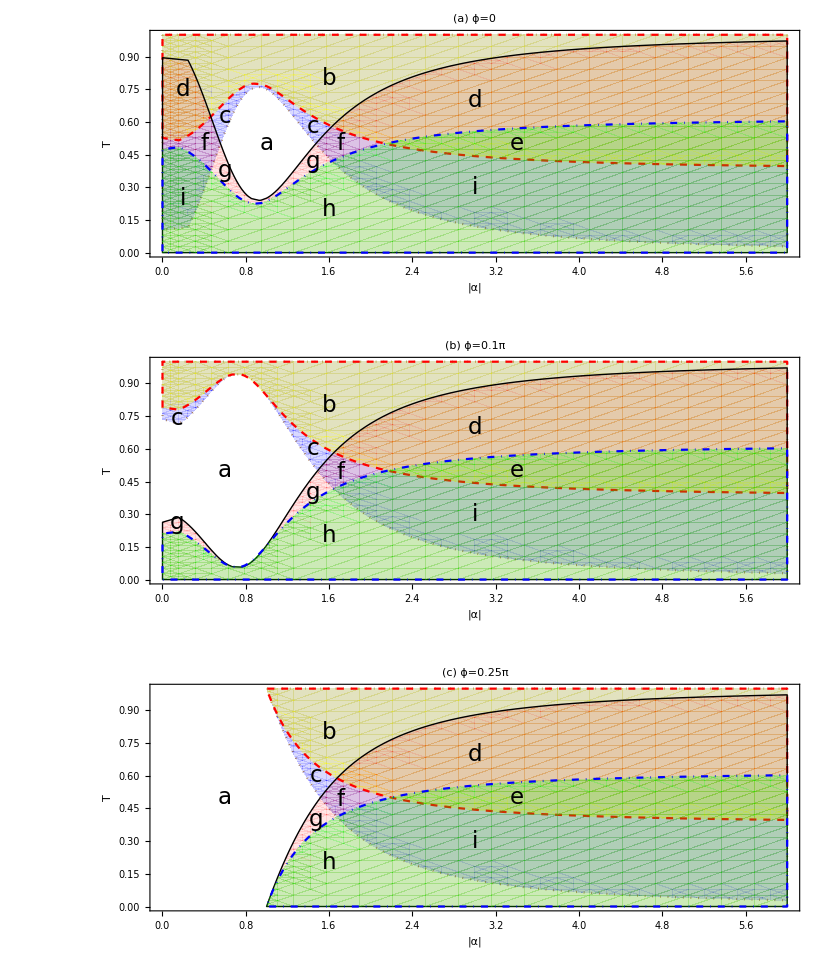
```mathematica
aa=-Graphics-
Export["G:\\11\\qq.pdf",aa]//ImageResolution->600
```

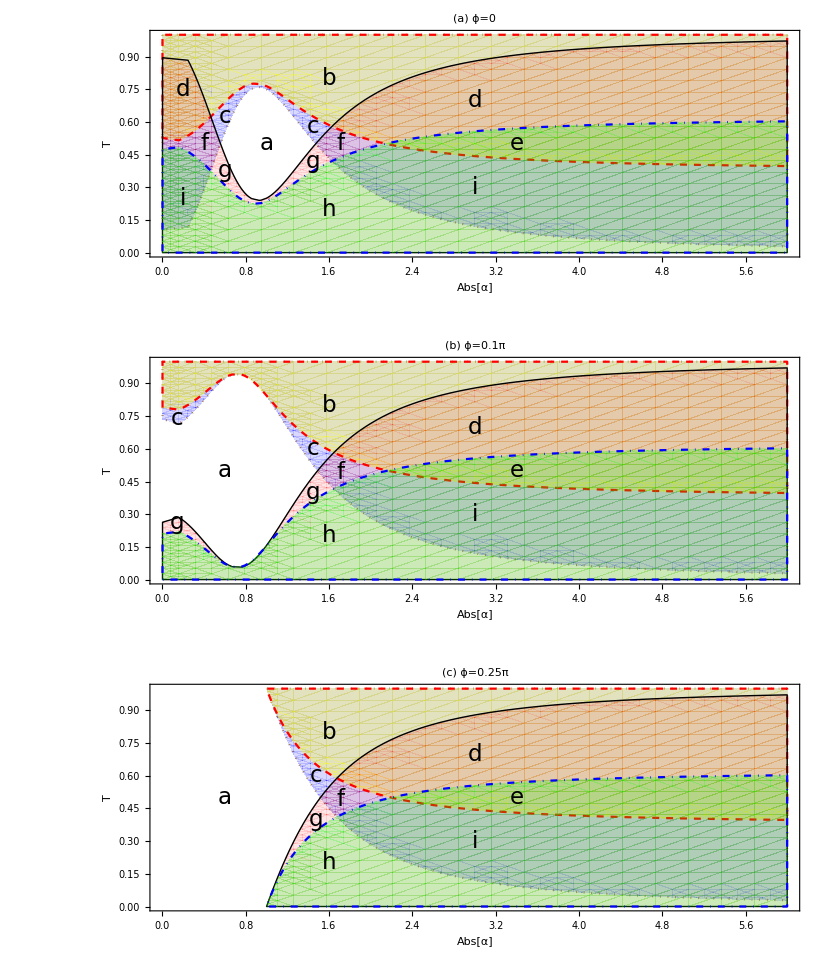

(ImageResolution→600)[G:\11\qq.pdf]